```mathematica
RealDigits[1/3, 2, 10, -1][[1]]
```

{0,1,0,1,0,1,0,1,0,1}

```mathematica
FromContinuedFraction[{0,1,0,1,0,1,1,0,1,1}]
```

3/10

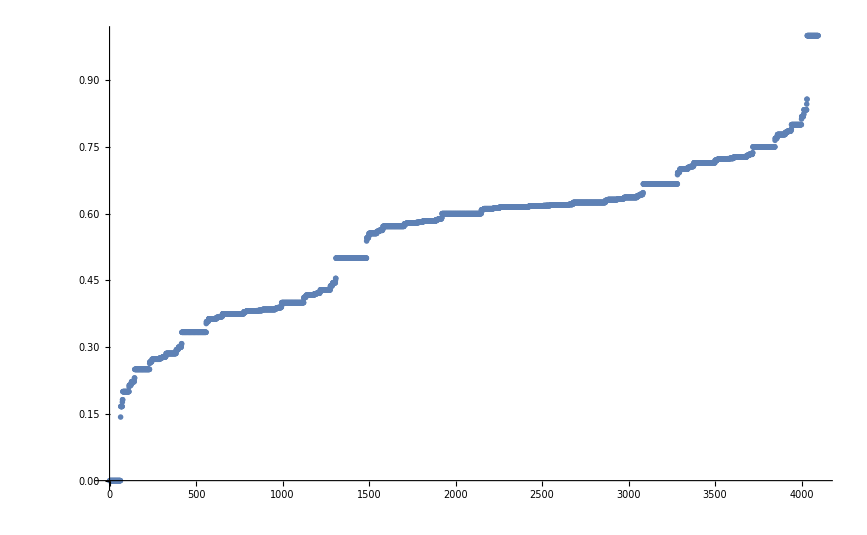

```mathematica
ListPlot[Sort[FromContinuedFraction/@Table[Join[{0},IntegerDigits[i,2]], {i,1,2^12}]]]
```

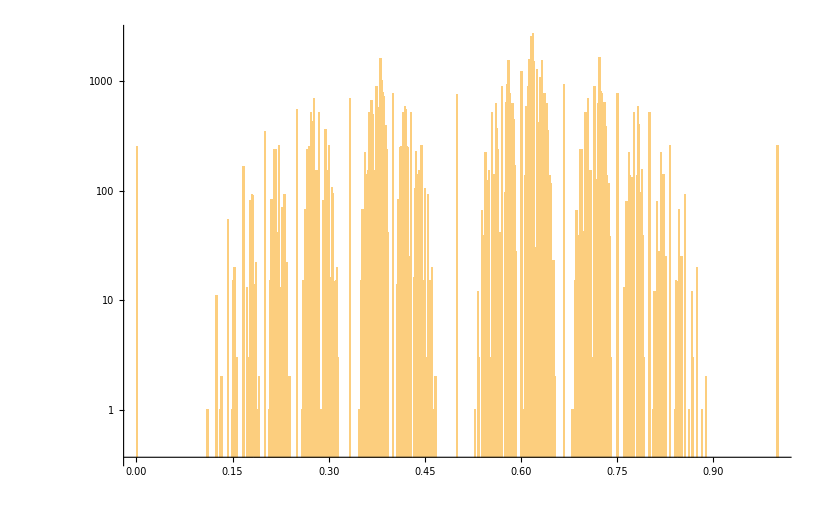

```mathematica
Histogram[FromContinuedFraction/@Table[Join[{0},IntegerDigits[i,2]], {i,1,2^16}],500,"LogCount"]
```